```mathematica
Clear["Global`*"]
```

```mathematica
χpp[t_]:=-I t^3/(1+t^4);
```

```mathematica
χ[t_]:=2I χpp[t]*HeavisideTheta[t]Exp[-10^-3 t]
```

```mathematica
χppF[ω_]:=Evaluate@FourierTransform[χpp[t],t,ω]
```

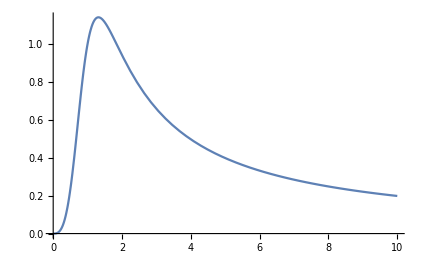

```mathematica
Plot[χ[t],{t,0,10}]
```

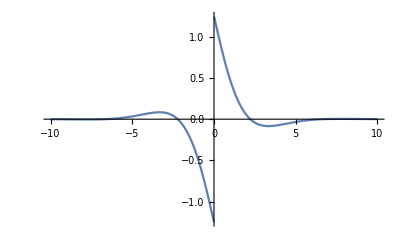

```mathematica
Plot[Re@χppF[ω],{ω,-10,10},PlotRange->All]
```

```mathematica
χspec[z_]:=Evaluate@Integrate[1/π*χppF[ωp]/(ωp-z),{ωp,-∞,∞}]
```

```mathematica
χω[ω_,η_]:=χspec[ω+I η]
```

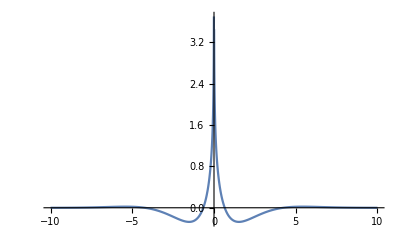

```mathematica
Plot[Re@χω[ω,10^-3],{ω,-10,10},PlotRange->All]
```

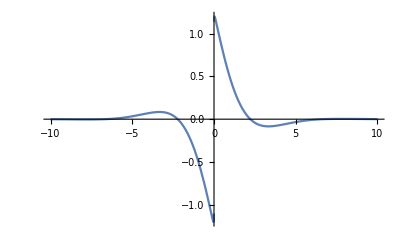

```mathematica
Plot[Im@χω[ω,10^-3],{ω,-10,10},PlotRange->All]
```

```mathematica
(*(Difficult step!)*)
χ2ω[ω_]:=Evaluate@FourierTransform[χ[t],t,ω]
```

```mathematica
Plot[Re@χ2ω[ω],{ω,-10,10},PlotRange->All]
Plot[Im@χ2ω[ω],{ω,-10,10},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
FourierTransform[HeavisideTheta[t],t,ω]
```

ⅈ/(√(2 π) ω)+√(π/2) DiracDelta[ω]